## TestFramework

Refactor format test result
runTest only catch assert-exceptions
write assertEquals to present both code and values of failed asserts

```mathematica
On[Assert]
```

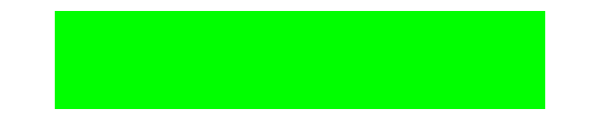
-Graphics-
12 run, 0 failed

```mathematica
ClearAll[AddTest,updateTestList,shouldBeAdded]
SetAttributes[AddTest,HoldAll]
AddTest[suite_,name_,test_]:=Module[{},
suite[name]:=test;
updateTestList[suite,name];
]
updateTestList[suite_,name_]:=(If[!ListQ@suite[UnitTests],suite[UnitTests]={}];
If[shouldBeAdded[suite,name],AppendTo[suite[UnitTests],name]])
shouldBeAdded[suite_,name_]:=Not@MemberQ[Join[suite[UnitTests],{"Set Up","Tear Down"}],name]

ClearAll[RunTest,runTest]
RunTest[suite_,name_]:=formatTestResult[{runTest[suite,name]}]
runTest[suite_,name_]:=Module[{result},
suite["Set Up"];
Block[{$AssertFunction = Throw[{##}]&},
result=Catch[suite[name];];
];
suite["Tear Down"];
If[result===Null,"Success",{suite,name,result}]
]
RunTest[suite_]:=formatTestResult[runTest[suite,#]&/@suite[UnitTests]]

ClearAll[formatTestResult]
formatTestResult[result:{__}]:=Module[{reportString,failures,nResults,nFailures},
nResults=Length@result;
failures=Cases[result,Except["Success"]];
nFailures=Length@failures;
reportString=ToString[nResults]<>" run, "<>ToString[nFailures]<>" failed";
If[nFailures>0,reportString=reportString<>StringJoin@@("\n"<>ToString[#[[2]]]<>" - Failed: "<>toString@@#[[3,1]]&/@failures);];
Column[{drawBar[nFailures>0],reportString}]
]
ClearAll[toString,drawBar]
toString[a_]:=ToString[Unevaluated[a]]
SetAttributes[toString,HoldAll]
drawBar[nFailuresNonZero_]:=Graphics[{If[nFailuresNonZero,Red,Green],Rectangle[{0,0},{15,1}]},Method->{"ShrinkWrap"->True},ImageSize->600]

ClearAll[DeleteTest]
DeleteTest[suite_,name_]:=(suite[name]=.;suite[UnitTests]=suite[UnitTests]/.name->Sequence[];)

RunTest[frameworkTests]
```

### Unit tests of the framework

```mathematica
Module[{mytests},
ClearAll[frameworkTests];
AddTest[frameworkTests,"Set Up",ClearAll[mytests]];
AddTest[frameworkTests,"Tear Down",ClearAll[mytests]];

AddTest[frameworkTests,"testAddSeveralTests",
AddTest[mytests,"aTest",1+1];
AddTest[mytests,"anotherTest",1+2];
Assert[mytests[UnitTests]==={"aTest","anotherTest"}];
];
AddTest[frameworkTests,"testAddTestDontEvaluateTheTest",
Module[{i=1},
AddTest[mytests,"aTest",Do[i++,{10}]];
Assert[i===1];
]];
AddTest[frameworkTests,"testAddingTwiceOverwrites",
AddTest[mytests,"aTest",1+1];
AddTest[mytests,"aTest",1+2];
Assert[mytests[UnitTests]==={"aTest"}];
];

AddTest[frameworkTests,"testRunTest",
Module[{i=1},
AddTest[mytests,"aTest",Do[i++,{10}]];
Assert[i===1];
RunTest[mytests,"aTest"];
Assert[i===11];
]];

AddTest[frameworkTests,"testSetUp",
mytests["isSetUp"]=False;
AddTest[mytests,"Set Up",mytests["isSetUp"]=True];
mytests["Set Up"];
Assert[TrueQ@mytests["isSetUp"]];
];
AddTest[frameworkTests,"testTearDown",
Module[{isStillSetUp},
mytests["Set Up"];
isStillSetUp=True;
AddTest[mytests,"Tear Down",Clear[isStillSetUp]];
mytests["Tear Down"];
Assert[Not@ValueQ[isStillSetUp]];
]];

AddTest[frameworkTests,"testRunTestOnSuite",
Module[{a,b,c},
AddTest[mytests,"test1",a=1];
AddTest[mytests,"test2",b=2];
AddTest[mytests,"test3",c=a+b];
RunTest[mytests];
Assert[a===1];
Assert[b===2];
Assert[c===3];
]];

AddTest[frameworkTests,"testDeleteTest",
AddTest[mytests,"aTest",a=1];
AddTest[mytests,"anotherTest",b=1];
DeleteTest[mytests,"aTest"];
Assert[mytests[UnitTests]==={"anotherTest"}];
];

AddTest[frameworkTests,"testFormatSingleSuccessfulTestResult",Module[{formattedResult},
AddTest[mytests,"aTest",Assert[1==1]];
formattedResult=RunTest[mytests,"aTest"];
Assert[MatchQ[formattedResult,Column[{_Graphics,"1 run, 0 failed"}]]]
]];
AddTest[frameworkTests,"testFormatTwoSuccessfulTestResult",Module[{formattedResult},
AddTest[mytests,"aTest",Assert[1==1]];
AddTest[mytests,"anotherTest",Assert[1==1]];
formattedResult=RunTest[mytests];
Assert[MatchQ[formattedResult,Column[{_Graphics,"2 run, 0 failed"}]]]
]];
AddTest[frameworkTests,"testFormatSingleFailedTestResult",Module[{formattedResult},
AddTest[mytests,"aTest",Assert[1==0]];
formattedResult=RunTest[mytests,"aTest"];
Assert[MatchQ[formattedResult,Column[{_Graphics,"1 run, 1 failed\naTest - Failed: Assert[1 == 0]"}]]]
]];
AddTest[frameworkTests,"testFormatOneEachTestResult",Module[{formattedResult},
AddTest[mytests,"aTest",Assert[1==1]];
AddTest[mytests,"anotherTest",Assert[1==-1]];
formattedResult=RunTest[mytests];
Assert[MatchQ[formattedResult,Column[{_Graphics,"2 run, 1 failed\nanotherTest - Failed: Assert[1 == -1]"}]]]
]];

]

RunTest[frameworkTests]
```

-Graphics-
12 run, 0 failed